## Solving Unstable Regions

```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/github/neuphysics/codebase/mma/dispersion-relation

```mathematica
Get["../../neupackage/mma/linearstability.wl"]
Get["../../neupackage/mma/dispersion-relation.wl"]
```

```mathematica
spectra={{{0.9,0.6},-1},{{0.6,0.3},1}}
```

{{{0.9,0.6},-1},{{0.6,0.3},1}}

```mathematica
colorf=Blend[{Blue,Red},#]&;
colorRainbow=ColorData["Rainbow"];
colorTemp=ColorData["Temperature"];
plotLegend[{min_,max_},n_,col_]:=Graphics[{{col[(#-1)/(n-1)],Rectangle[{0,#-1},{1,#}]},{Black,Text[NumberForm[Rescale[#,{1,n},{min,max}],{4,2}],{3,#-.5},{1,0}]}}&/@Range@n,Frame->True,FrameTicks->None,PlotRangePadding->.5]
```

```mathematica
Needs["ErrorBarPlots`"]
```

Testing Function

```mathematica
ConAxialSymOmegaKMZAEqn[omegaR_,omegaI_,kR_,kI_,spect_:{{{0.9,0.6},-1},{{0.6,0.3},1}}]:=Module[{eqnLHSM,spectM},


spectM=spect;

eqnLHSM[omega_,k_]=(omega-#)&/@ConAxialSymOmegaNMZA[k/omega,spectM];

Transpose[
{(#==0)&/@ComplexExpand[Re[
eqnLHSM[omegaR+I omegaI,kR+I kI]
]],
(#==0)&/@ComplexExpand[Im[
eqnLHSM[omegaR+I omegaI,kR+I kI]
]]
}
]

]
```

```mathematica
ConAxialSymOmegaKMZAEqn[1,0,kreal,kimag]
```

{{1-(0.0225 5)/1+17+1+1/4 Cos[1/2 Arg[(1) (1)]] √(√((-(0.09 kimag)/(kimag^2+1)+20)^2+(1)^2) √((1)^2+(1)^2))==0,1},1}
 |  |  |  |

```mathematica
FindRoot[ConAxialSymOmegaKMZAEqn[0.8,0,kreal,kimag][[1]],{{kreal,1},{kimag,1}}]
FindRoot[ConAxialSymOmegaKMZAEqn[0.8,0,kreal,kimag][[2]],{{kreal,1},{kimag,1}}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{kreal→2.10241,kimag→0.000416557}

{kreal→2.67042,kimag→-9.95832×10^-16}

```mathematica
FindRoot[ConAxialSymOmegaKMZAEqn[omegareal,omegaimag,-2,0,spectBox2][[1]],{{omegareal,-2*0.6,-10,-0.5},{omegaimag,1}}]
```

FindRoot::reged: The point {-0.5, 0.371569} is at the edge of the search region {-10., -0.5} in coordinate 1 and the computed search direction points outside the region.

{omegareal→-0.5,omegaimag→0.371569}

```mathematica
{omega,ConAxialSymOmegaNMZA[-2/omega,spectBox2][[1]]}/.FindRoot[ConAxialSymOmegaNMZA[-2/omega,spectBox2][[1]]==omega,{omega,-1.2-1I}]
```

{3.89577×10^-17-8.40982×10^-18 ⅈ,2.62964×10^-18-5.67663×10^-19 ⅈ}

## Solving Continuous Spectrum

Solve box spectrum

```mathematica
spectBox={{{0.9,0.3},1}}
spectBox2={{{0.9,0.6},3},{{0.6,0.3},-3}}
```

{{{0.9,0.3},1}}

{{{0.9,0.6},3},{{0.6,0.3},-3}}

They can both be imaginary.

```mathematica
Table[
{{omegareal,omegaimag},{kreal,kimag}}/.FindRoot[
ConAxialSymOmegaKMZAEqn[omegareal,omegaimag,kreal,kimag,spectBox][[#]],
{{kreal,1},{kimag,1}}
]&/@{1,2},
{omegareal,{-1,1}},
{omegaimag,{-1,1}}
]
```

```mathematica
Table[
{{omegareal,omegaimag},{kreal,kimag}}/.FindRoot[
ConAxialSymOmegaKMZAEqn[omegareal,omegaimag,kreal,kimag,spectBox2][[#]],
{{kreal,1},{kimag,1}}
]&/@{1,2},
{omegareal,{-1,1}},
{omegaimag,{-1,1}}
]//Grid
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{{{-1,-1},{-3.32423,-3.14419}},{{-1,-1},{-5.23708,-1.23846}}} | {{{-1,1},{-3.32423,3.14419}},{{-1,1},{-5.37005,1.17151}}}
{{{1,-1},{0.293735,-0.293735}},{{1,-1},{1.72345,-2.27358}}} | {{{1,1},{0.35732,0.35732}},{{1,1},{1.,1.}}}

Fix omega to be real, generate a list of omega’s

```mathematica
listofOmega=Table[i,{i,-4,4,0.1}];
1+Floor[Length@listofOmega/2];
listofOmega=Drop[listofOmega,{1+Floor[Length@listofOmega/2]}];
```

Fix k to be real, generate a list of k’s.

```mathematica
listofK=Table[i,{i,-4,4,0.1}];
listofK=Drop[listofK,{1+Floor[Length@listofK/2]}];
```

## spectBox

Calculate spectBox

```mathematica
NSolve[
ConAxialSymOmegaKMZAEqn[omegareal,omegaimag,1,0,spectBox][[1]],
{omegareal,omegaimag}
]
```

$Aborted

```mathematica
omegakSpectBoxOmegaReal=Table[
{{omegareal,0},{kreal,kimag}}/.FindRoot[
ConAxialSymOmegaKMZAEqn[omegareal,0,kreal,kimag,spectBox][[#]],
{{kreal,omegareal/0.6},{kimag,omegareal/0.6}}
]&/@{1,2},
{omegareal,listofOmega}
];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

FindRoot::jsing: Encountered a singular Jacobian at the point {kreal, kimag} = {1.07618, 1244.88}. Try perturbing the initial point(s).

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

Each of the solutions contains two sets, the first one is for MZA+ while the second one is for MZA-.

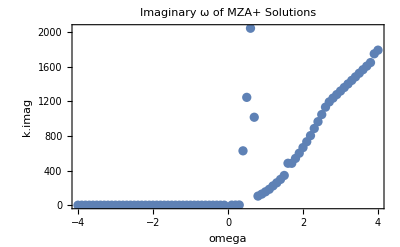

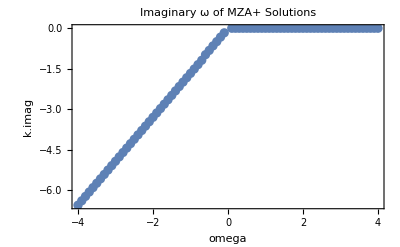

```mathematica
{#[[1,1]],#[[2,1]]}&/@(#[[1]]&/@omegakSpectBoxOmegaReal);
{#[[1,1]],#[[2,2]]}&/@(#[[1]]&/@omegakSpectBoxOmegaReal);
ListPlot[%,Frame->True,PlotLabel->"Imaginary ω of MZA+ Solutions",FrameLabel->{"omega","k.imag"},PlotRange->Full]

{#[[1,1]],#[[2,1]]}&/@(#[[2]]&/@omegakSpectBoxOmegaReal);
{#[[1,1]],#[[2,2]]}&/@(#[[2]]&/@omegakSpectBoxOmegaReal);
ListPlot[%,Frame->True,PlotLabel->"Imaginary ω of MZA+ Solutions",FrameLabel->{"omega","k.imag"},PlotRange->Full]
```

This is a weird result

```mathematica
{omegareal/0.9,{omegareal,0},{kreal,kimag}}/.FindRoot[
ConAxialSymOmegaKMZAEqn[omegareal,0,kreal,kimag,spectBox][[1]],
{{kreal,omegareal/1.9},{kimag,omegareal/0.9}}
]/.omegareal->-1.5
```

FindRoot::srect: Value 0.526316\ omegareal in search specification {kreal, omegareal/1.9} is not a number or array of numbers.

ReplaceAll::reps: {FindRoot[ConAxialSymOmegaKMZAEqn[omegareal, 0, kreal, kimag, spectBox] ⟦ 1 ⟧, {{kreal, omegareal/1.9}, {kimag, omegareal/0.9}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{-1.66667,{-1.5,0},{-1.66663,-2.44522×10^-17}}

```mathematica
omegakSpectBoxKReal=Table[
{{omegareal,omegaimag},{kreal,0}}/.FindRoot[
ConAxialSymOmegaKMZAEqn[omegareal,omegaimag,kreal,0,spectBox][[#]],
{{omegareal,0.6kreal},{omegaimag,0.6kreal}}
]&/@{1,2},
{kreal,listofK}
];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
{{omegareal,omegaimag},{kreal,0}}/.FindRoot[
ConAxialSymOmegaKMZAEqn[omegareal,omegaimag,kreal,0,spectBox][[1]],
{{omegareal,0.9kreal},{omegaimag,0.9kreal}}
]/.kreal->0.3
```

FindRoot::srect: Value 0.9\ kreal in search specification {omegareal, 0.9\ kreal} is not a number or array of numbers.

ReplaceAll::reps: {FindRoot[ConAxialSymOmegaKMZAEqn[omegareal, omegaimag, kreal, 0, spectBox] ⟦ 1 ⟧, {{omegareal, 0.9\ kreal}, {omegaimag, 0.9\ kreal}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{{-0.0431336,-6.45327×10^-22},{0.3,0}}

MZA+ solutions for spectBox

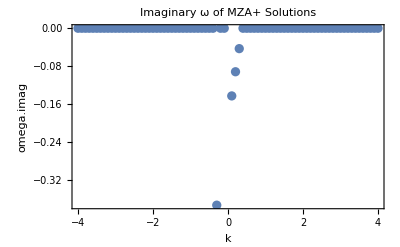

```mathematica
{#[[2,1]],#[[1,1]]}&/@(#[[1]]&/@omegakSpectBoxKReal);
ListPlot[%,Frame->True,PlotLabel->"Imaginary ω of MZA+ Solutions",FrameLabel->{"k","omega.imag"},PlotRange->Full]
```

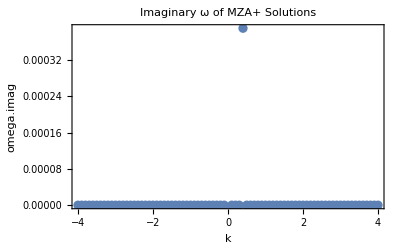

```mathematica
{#[[2,1]],#[[1,1]]}&/@(#[[1]]&/@omegakSpectBoxKReal);
{#[[2,1]],#[[1,2]]}&/@(#[[1]]&/@omegakSpectBoxKReal);
ListPlot[%,Frame->True,PlotLabel->"Imaginary ω of MZA+ Solutions",FrameLabel->{"k","omega.imag"},PlotRange->Full]
```

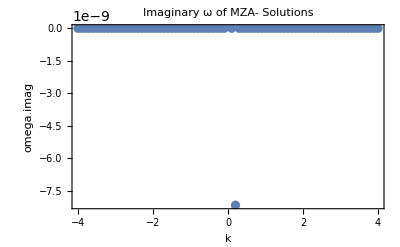

```mathematica
{#[[2,1]],#[[1,1]]}&/@(#[[2]]&/@omegakSpectBoxKReal);
{#[[2,1]],#[[1,2]]}&/@(#[[2]]&/@omegakSpectBoxKReal);
ListPlot[%,Frame->True,PlotLabel->"Imaginary ω of MZA- Solutions",FrameLabel->{"k","omega.imag"},PlotRange->Full]
```

```mathematica
lsaGraphc93OmegaRealMZAp={#[[2,1]],#[[1,1]],#[[2,2]]}&/@(#[[1]]&/@omegakSpectBoxOmegaReal);
lsaGraphc93OmegaRealMZApRange=Select[lsaGraphc93OmegaRealMZAp,(-4<#[[1]]<4)&&(-4<#[[2]]<4)&];

lsaGraphc93OmegaRealMZAm={#[[2,1]],#[[1,1]],#[[2,2]]}&/@(#[[2]]&/@omegakSpectBoxOmegaReal);
lsaGraphc93OmegaRealMZAmRange=Select[lsaGraphc93OmegaRealMZAp,(-4<#[[2]]<4)&&(-4<#[[2]]<4)&];

lsaGraphc93KRealMZAp={#[[2,1]],#[[1,1]],#[[1,2]]}&/@(#[[1]]&/@omegakSpectBoxKReal);
lsaGraphc93KRealMZApRange=Select[lsaGraphc93KRealMZAp,(-4<#[[1]]<4)&&(-4<#[[2]]<4)&];

lsaGraphc93KRealMZAm={#[[2,1]],#[[1,1]],#[[1,2]]}&/@(#[[2]]&/@omegakSpectBoxKReal);
lsaGraphc93KRealMZAmRange=Select[lsaGraphc93KRealMZAp,(-4<#[[2]]<4)&&(-4<#[[2]]<4)&];
```

Select::normal: Nonatomic expression expected at position 1 in Select[omegakSpectBoxKReal, -4 < #1 ⟦ 1 ⟧ < 4 && -4 < #1 ⟦ 2 ⟧ < 4 &].

Select::normal: Nonatomic expression expected at position 1 in Select[omegakSpectBoxKReal, -4 < #1 ⟦ 2 ⟧ < 4 && -4 < #1 ⟦ 2 ⟧ < 4 &].

```mathematica
Export["export/unstable-regions/lsaGraphc93KRealMZAp.csv",lsaGraphc93KRealMZAp]
```

export/unstable-regions/lsaGraphc93KRealMZAp.csv

```mathematica
Export["export/unstable-regions/lsaGraphc93KRealMZAm.csv",lsaGraphc93KRealMZAm]
```

export/unstable-regions/lsaGraphc93KRealMZAm.csv

```mathematica
Export["export/unstable-regions/lsaGraphc93OmegaRealMZAp.csv",lsaGraphc93OmegaRealMZAp]
```

export/unstable-regions/lsaGraphc93OmegaRealMZAp.csv

```mathematica
Export["export/unstable-regions/lsaGraphc93OmegaRealMZAm.csv",lsaGraphc93OmegaRealMZAm]
```

export/unstable-regions/lsaGraphc93OmegaRealMZAm.csv

## spectBox2

Calculate spectBox2

```mathematica
omegakSpectBox2OmegaReal=Table[
{{omegareal,0},{kreal,kimag}}/.FindRoot[
ConAxialSymOmegaKMZAEqn[omegareal,0,kreal,kimag,spectBox2][[#]],
{{kreal,omegareal/0.6},{kimag,omegareal/0.6}}
]&/@{1,2},
{omegareal,listofOmega}
];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

$Aborted

```mathematica
omegakSpectBox2KReal=Table[
{{omegareal,omegaimag},{kreal,0}}/.FindRoot[
ConAxialSymOmegaKMZAEqn[omegareal,omegaimag,kreal,0,spectBox2][[#]],
{{omegareal,kreal 0.6},{omegaimag,kreal 0.6}}
]&/@{1,2},
{kreal,listofK}
];
```

## The Old School

The MZA+ solutions spectBox2 are

```mathematica
{#[[1,1]],#[[2,1]]}&/@(#[[1]]&/@omegakSpectBox2OmegaReal);
{#[[1,1]],#[[2,2]]}&/@(#[[1]]&/@omegakSpectBox2OmegaReal);
ListPlot[%,Frame->True,PlotLabel->"Imaginary k of MZA+ Solutions",FrameLabel->{"omega","k.imag"}]
```

ListPlot::lpn: omegakSpectBox2Ex1 is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot[omegakSpectBox2Ex1,Frame→True,PlotLabel→Imaginary k of MZA+ Solutions,FrameLabel→{omega,k.imag}]

```mathematica
{{omegareal,0},{kreal,kimag}}/.FindRoot[
ConAxialSymOmegaKMZAEqn[omegareal,0,kreal,kimag,spectBox2][[1]],
{{kreal,1},{kimag,1}}
]/.omegareal->2
```

FindRoot::nlnum: The function value {1.03375\ omegareal - 0.375\ omegareal\ Arg[1.  - (0.9  + 0.9\ ⅈ)\ Power[« 2 »]/1.  + Times[« 2 »]] + « 10 » + 0.25\ Cos[0.5\ Arg[Plus[« 5 »]\ Plus[« 5 »]]]\ √√Power[« 2 »] + Power[« 2 »]\ √Power[« 2 »] + Power[« 2 »], « 1 »} is not a list of numbers with dimensions {2} at {kreal, kimag} = {1., 1.}.

ReplaceAll::reps: {FindRoot[ConAxialSymOmegaKMZAEqn[omegareal, 0, kreal, kimag, spectBox2] ⟦ 1 ⟧, {{kreal, 1}, {kimag, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{{2,0},{-1.88622,-0.00930305}}

The MZA- solution

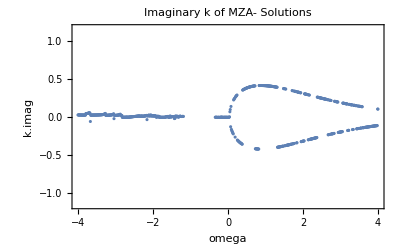

```mathematica
{#[[1,1]],#[[2,2]]}&/@(#[[2]]&/@omegakSpectBox2OmegaReal);
ListPlot[%,Frame->True,PlotLabel->"Imaginary k of MZA- Solutions",FrameLabel->{"omega","k.imag"}]
```

MZA+ solution

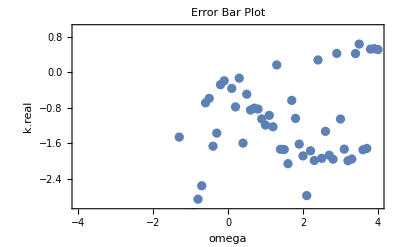

```mathematica
{{#[[1,1]],#[[2,1]]},ErrorBar[0,#[[2,2]] ]}&/@(#[[1]]&/@omegakSpectBox2OmegaReal);
ErrorListPlot[%,PlotRange->{Automatic,{-3,1}},Frame->True,PlotLabel->"Error Bar Plot",FrameLabel->{"omega","k.real"}]
```

```mathematica
graphicMZAp={#[[2,1]],#[[1,1]],#[[2,2]]}&/@(#[[1]]&/@omegakSpectBox2OmegaReal);
graphicMZApRange=Select[graphicMZAp,(-4<#[[1]]<4)&&(-4<#[[2]]<4)&];
```

```mathematica
graphicMZAm={#[[2,1]],#[[1,1]],#[[2,2]]}&/@(#[[2]]&/@omegakSpectBox2OmegaReal);
graphicMZAmRange=Select[graphicMZAm,(-4<#[[1]]<4)&&(-4<#[[2]]<4)&];
```

## Simplified Procedure

### For Real Omega

```mathematica
omegakSpectBox2OmegaRealMZAm=Table[
{{omegareal,0},{kreal,kimag}}/.FindRoot[
ConAxialSymOmegaKMZAEqn[omegareal,0,kreal,kimag,spectBox2][[2]],
{{kreal,omegareal/0.6,0,10},{kimag,omegareal/0.6,0,10}}
],
{omegareal,Select[listofOmega,#>0&]}
];
```

FindRoot::reged: The point {0., 0.277165} is at the edge of the search region {0., 10.} in coordinate 1 and the computed search direction points outside the region.

```mathematica
omegakSpectBox2OmegaRealMZAp=Table[
{{omegareal,0},{kreal,kimag}}/.FindRoot[
ConAxialSymOmegaKMZAEqn[omegareal,0,kreal,kimag,spectBox2][[1]],
{{kreal,omegareal/0.6},{kimag,omegareal/0.6}}
],
{omegareal,Select[listofOmega,#<0&]}
];
```

```mathematica
omegakSpectBox2OmegaRealMZApPoints={#[[2,1]],#[[1,1]],#[[2,2]]}&/@(omegakSpectBox2OmegaRealMZAp);
omegakSpectBox2OmegaRealMZApPointsClean=Select[omegakSpectBox2OmegaRealMZApPoints,(-4<#[[1]]<4)&&(-4<#[[2]]<4)&];
```

```mathematica
Graphics[
{Point[{#[[1]],#[[2]]}&/@omegakSpectBox2OmegaRealMZApPointsClean,VertexColors->colorf/@Rescale@(#[[3]]&/@omegakSpectBox2OmegaRealMZApPointsClean)],Inset[plotLegend[{Min@#,Max@#}&@(#[[3]]&/@omegakSpectBox2OmegaRealMZApPointsClean),20,colorf],Scaled[{1,1/2}],ImageScaled[{-0.1,1/2}],Scaled[{1/4,0.9}]]
},Axes->True,Frame->True,ImageSize->Large,FrameLabel->{"k.real","omega"},PlotLabel->"k.imag values for different omega and k.real values"
]
```

-Graphics-

MZA- solution

```mathematica
omegakSpectBox2OmegaRealMZAmPoints={#[[2,1]],#[[1,1]],#[[2,2]]}&/@(omegakSpectBox2OmegaRealMZAm);
omegakSpectBox2OmegaRealMZAmPointsClean=Select[omegakSpectBox2OmegaRealMZAmPoints,(-4<#[[1]]<4)&&(-4<#[[2]]<4)&];
```

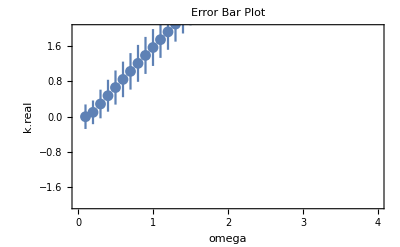

```mathematica
{{#[[1,1]],#[[2,1]]},ErrorBar[0,#[[2,2]] ]}&/@(omegakSpectBox2OmegaRealMZAm);
ErrorListPlot[%,PlotRange->{Automatic,{-2,2}},Frame->True,PlotLabel->"Error Bar Plot",FrameLabel->{"omega","k.real"}]
```

```mathematica
Graphics[
{Point[{#[[1]],#[[2]]}&/@omegakSpectBox2OmegaRealMZAmPointsClean,VertexColors->colorf/@Rescale@(#[[3]]&/@omegakSpectBox2OmegaRealMZAmPointsClean)],Inset[plotLegend[{Min@#,Max@#}&@(#[[3]]&/@omegakSpectBox2OmegaRealMZAmPointsClean),20,colorf],Scaled[{1,1/2}],ImageScaled[{-0.1,1/2}],Scaled[{1/4,0.9}]]
},Axes->True,Frame->True,ImageSize->Large,FrameLabel->{"k.real","omega"},PlotLabel->"k.imag values for different omega and k.real values"
]
```

-Graphics-

### For Real K

```mathematica
omegakSpectBox2KRealMZAp=Table[
{{omegareal,omegaimag},{kreal,0}}/.FindRoot[
ConAxialSymOmegaKMZAEqn[omegareal,omegaimag,kreal,0,spectBox2][[1]],
{{omegareal,kreal 0.3},{omegaimag,0.1}}
],
{kreal,listofK}
];
```

```mathematica
omegakSpectBox2KRealMZAm=Table[
{{omegareal,omegaimag},{kreal,0}}/.FindRoot[
ConAxialSymOmegaKMZAEqn[omegareal,omegaimag,kreal,0,spectBox2][[2]],
{{omegareal,kreal 0.3},{omegaimag,0.1}}
],
{kreal,listofK}
];
```

```mathematica
omegakSpectBox2KRealMZApPoints={#[[2,1]],#[[1,1]],#[[2,2]]}&/@(omegakSpectBox2KRealMZAp);
omegakSpectBox2KRealMZApPointsClean=Select[omegakSpectBox2KRealMZApPoints,(-4<#[[1]]<4)&&(-4<#[[2]]<4)&];
```

```mathematica
Export["export/unstable-regions/lsaGraphc963-omegakKRealMZApPoints.csv",omegakSpectBox2KRealMZApPoints]
```

export/unstable-regions/lsaGraphc963-omegakKRealMZApPoints.csv

## Export Data

```mathematica
Export["export/unstable-regions/lsaGraphc963MZAm.csv",omegakSpectBox2OmegaRealMZAmPoints](* {k.real,omega,k.imag} *)
```

export/unstable-regions/lsaGraphc963MZAm.csv

```mathematica
Export["export/unstable-regions/lsaGraphc963MZAp.csv",omegakSpectBox2OmegaRealMZApPoints](* {k.real,omega,k.imag} *)
```

export/unstable-regions/lsaGraphc963MZAp.csv

```mathematica
Show[
Graphics[
{Point[{#[[1]],#[[2]]}&/@Select[Import["graphicMZAp.csv"],(-4<#[[1]]<4)&&(-4<#[[2]]<4)&],VertexColors->colorf/@Rescale@(#[[3]]&/@Select[Import["graphicMZAp.csv"],(-4<#[[1]]<4)&&(-4<#[[2]]<4)&])],Inset[plotLegend[{Min@#,Max@#}&@(#[[3]]&/@Select[Import["graphicMZAp.csv"],(-4<#[[1]]<4)&&(-4<#[[2]]<4)&]),20,colorf],Scaled[{1,1/2}],ImageScaled[{-0.1,1/2}],Scaled[{1/4,0.9}]]
},Axes->True,Frame->True,ImageSize->Large,FrameLabel->{"k.real","omega"},PlotLabel->"k.imag values for different omega and k.real values"
],
Plot[{0.9x,0.6x,0.3x},{x,-4,4},PlotStyle->Directive[LightGray,Dashing[0.03]],Frame->True,ImageSize->Large,PlotRange->{{-2,2},{-2,2}},PlotLabel->"MZA and MAA Dispersion Relation with Crossing"]
]
```

-Graphics-

```mathematica
Select[Import["export/unstable-regions/lsaGraphc963MZAm.csv"],(-4<#[[1]]<4)&&(-4<#[[2]]<4)&]//Length
Select[Import["export/unstable-regions/lsaGraphc963MZAp.csv"],(-4<#[[1]]<4)&&(-4<#[[2]]<4)&&(-1<##[[3]]<1)&]//Length
```

334

329

```mathematica
Show[
Graphics[
{Point[{#[[1]],#[[2]]}&/@Select[Import["graphicMZAm.csv"],(-4<#[[1]]<4)&&(-4<#[[2]]<4)&&(-1<##[[3]]<1)&],VertexColors->colorf/@Rescale@(#[[3]]&/@Select[Import["graphicMZAm.csv"],(-4<#[[1]]<4)&&(-4<#[[2]]<4)&&(-1<##[[3]]<1)&])],Inset[plotLegend[{Min@#,Max@#}&@(#[[3]]&/@Select[Import["graphicMZAm.csv"],(-4<#[[1]]<4)&&(-4<#[[2]]<4)&&(-1<##[[3]]<1)&]),20,colorf],Scaled[{1,1/2}],ImageScaled[{-0.1,1/2}],Scaled[{1/4,0.9}]]
},Axes->True,Frame->True,ImageSize->Large,FrameLabel->{"k.real","omega"},PlotLabel->"k.imag values for different omega and k.real values"
],
Plot[{0.9x,0.6x,0.3x},{x,-4,4},PlotStyle->Directive[LightGray,Dashing[0.03]],Frame->True,ImageSize->Large,PlotRange->{{-2,2},{-2,2}},PlotLabel->"MZA and MAA Dispersion Relation with Crossing"]
]
```

-Graphics-

## Draft

isotropic case

```mathematica
i0mi2[nr_,ni_,c1_,c2_]:=-1/(nr+I ni)((c2-c1)(1/(nr+I ni)+c1+c2))+1/(nr+I ni)(1-(1/(nr+I ni))^2)Log[(1-c2 (nr+I ni))/(1-c1((nr+I ni)))]
```

```mathematica
eqnHR[nr_,ni_,c1_,c2_]:=ComplexExpand[
Re[
i0mi2[nr,ni,c1,c2]+4
]
]==0
eqnHI[nr_,ni_,c1_,c2_]:=ComplexExpand[
Im[
i0mi2[nr,ni,c1,c2]+4
]
]==0
```

```mathematica
eqnH[nr_,ni_,c1_,c2_]:=i0mi2[nr,ni,c1,c2]+4==0
```

```mathematica
FindRoot[eqnHR[nreal,nimag,0.9,0.3]&&eqnHI[nreal,nimag,0.9,0.3],{{nreal,1},{nimag,1}}]
```

{nreal→3.33333,nimag→1.1682×10^-20}

box spectrum

```mathematica
eqnBR[nr_,ni_,c1_,c2_,c0_,g1_,g2_]:=ComplexExpand[
Re[
g1 i0mi2[nr,ni,c1,c0]+g2 i0mi2[nr,ni,c0,c2]+4
]
]==0
eqnBI[nr_,ni_,c1_,c2_,c0_,g1_,g2_]:=ComplexExpand[
Im[
g1 i0mi2[nr,ni,c1,c0]+g2 i0mi2[nr,ni,c0,c2]+4
]
]==0
```

```mathematica
rootB[g1_,g2_]:=FindRoot[eqnBR[nreal,nimag,0.9,0.3,0.6,g1,g2]&&eqnBI[nreal,nimag,0.9,0.3,0.6,g1,g2],{{nreal,1},{nimag,1}}]
```

```mathematica
{nreal,nimag}/.rootB[3,-3]
```

{1.65241,0.130125}

```mathematica
Table[
Join[{{g1,g2}},{{nreal,nimag}/.rootB[g1,g2]}],
{g1,-3,3,1},{g2,-3,3,1}
]//Grid//Quiet
```

FindRoot::nlnum: The function value {False} is not a list of numbers with dimensions {1} at {nreal, nimag} = {1., 1.}.

ReplaceAll::reps: {FindRoot[eqnBR[nreal, nimag, 0.9, 0.3, 0.6, 0, 0] && eqnBI[nreal, nimag, 0.9, 0.3, 0.6, 0, 0], {{nreal, 1}, {nimag, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{{-3,-3},{1.00654,1.14531×10^-16}} | {{-3,-2},{0.321178,3.047×10^-24}} | {{-3,-1},{0.248348,-5.77446×10^-28}} | {{-3,0},{0.190081,6.4323×10^-23}} | {{-3,1},{0.1413,6.94329×10^-24}} | {{-3,2},{0.0992947,-1.68554×10^-38}} | {{-3,3},{3.3486,-1.08293×10^-41}}
{{-2,-3},{0.300018,8.03454×10^-22}} | {{-2,-2},{0.227576,1.65263×10^-22}} | {{-2,-1},{0.169586,-4.89252×10^-27}} | {{-2,0},{1.11098,-5.22748×10^-15}} | {{-2,1},{0.0793074,-3.23324×10^-16}} | {{-2,2},{3.33467,-7.04659×10^-29}} | {{-2,3},{3.3491,-5.41841×10^-30}}
{{-1,-3},{1.11107,5.89803×10^-15}} | {{-1,-2},{1.11111,1.22311×10^-17}} | {{-1,-1},{1.11111,1.00942×10^-23}} | {{-1,0},{0.0582099,-6.47019×10^-17}} | {{-1,1},{3.33333,-2.53978×10^-25}} | {{-1,2},{3.33474,7.79571×10^-14}} | {{-1,3},{3.34963,-2.43777×10^-22}}
{{0,-3},{1.61177,4.79668×10^-24}} | {{0,-2},{1.65739,-3.5937×10^-16}} | {{0,-1},{1.66662,-5.9501×10^-14}} | {{0,0},{nreal,nimag}/.FindRoot[eqnBR[nreal,nimag,0.9,0.3,0.6,0,0]&&eqnBI[nreal,nimag,0.9,0.3,0.6,0,0],{{nreal,1},{nimag,1}}]} | {{0,1},{3.33333,-2.08489×10^-19}} | {{0,2},{3.33481,4.7401×10^-17}} | {{0,3},{-0.086448,-3.2449×10^-19}}
{{1,-3},{1.6081,0.0575407}} | {{1,-2},{1.65157,0.0255526}} | {{1,-1},{1.66665,0.00396108}} | {{1,0},{-0.0545573,-1.96916×10^-23}} | {{1,1},{3.33333,1.45913×10^-20}} | {{1,2},{3.33488,3.33081×10^-18}} | {{1,3},{3.35072,-6.11532×10^-17}}
{{2,-3},{1.62757,0.0995193}} | {{2,-2},{1.66408,-0.0537959}} | {{2,-1},{-0.0784544,-4.89636×10^-23}} | {{2,0},{-0.106142,6.16686×10^-26}} | {{2,1},{3.33333,8.18405×10^-20}} | {{2,2},{3.33496,-4.33242×10^-16}} | {{2,3},{-0.174874,7.98958×10^-26}}
{{3,-3},{1.65241,0.130125}} | {{3,-2},{1.6845,0.0769379}} | {{3,-1},{-0.130767,-7.03062×10^-30}} | {{3,0},{-0.155246,-9.41205×10^-26}} | {{3,1},{3.33333,1.59615×10^-19}} | {{3,2},{-0.197923,5.44514×10^-17}} | {{3,3},{3.35188,8.77362×10^-20}}

This indicates that {g1,g2}={3,-3} has a large imaginary part of n.

To have a better understanding, I can make a heat map.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot :: cvmit will be suppressed during this calculation.

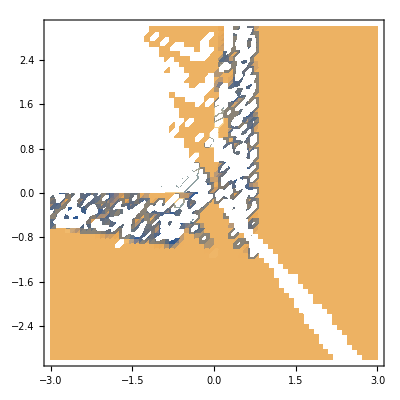

```mathematica
ListDensityPlot[
Table[
First@{nimag}/.rootB[g1,g2]
,
{g1,-3,3,0.09},{g2,-3,3,0.09}
],
DataRange->{{-3,3},{-3,3}}
]
```

Some Examples of ComplexExpand

Examples of finding the imaginary and real part of the equation

```mathematica
ComplexExpand[(x+I y)^6]
```

x^6-15 x^4 y^2+15 x^2 y^4-y^6+ⅈ (6 x^5 y-20 x^3 y^3+6 x y^5)

```mathematica
ComplexExpand[Re[(x+I y)^6]]
```

x^6-15 x^4 y^2+15 x^2 y^4-y^6

```mathematica
ComplexExpand[
Re[
Log@(1-c2 (nr+I ni))/(1-c1(nr+I ni))
]
]
ComplexExpand[
Im[
Log@(1-c2 (nr+I ni))/(1-c1(nr+I ni))
]
]
```

-(c1 ni Arg[1-c2 (ⅈ ni+nr)])/(c1^2 ni^2+(1-c1 nr)^2)+Log[c2^2 ni^2+(1-c2 nr)^2]/(2 (c1^2 ni^2+(1-c1 nr)^2))-(c1 nr Log[c2^2 ni^2+(1-c2 nr)^2])/(2 (c1^2 ni^2+(1-c1 nr)^2))

Arg[1-c2 (ⅈ ni+nr)]/(c1^2 ni^2+(1-c1 nr)^2)-(c1 nr Arg[1-c2 (ⅈ ni+nr)])/(c1^2 ni^2+(1-c1 nr)^2)+(c1 ni Log[c2^2 ni^2+(1-c2 nr)^2])/(2 (c1^2 ni^2+(1-c1 nr)^2))

```mathematica
ComplexExpand[
Im[
Log@(1-c2 (nr+I ni))/(1-c1(nr+I ni))
]
]
```

Arg[1-c2 (ⅈ ni+nr)]/(c1^2 ni^2+(1-c1 nr)^2)-(c1 nr Arg[1-c2 (ⅈ ni+nr)])/(c1^2 ni^2+(1-c1 nr)^2)+(c1 ni Log[c2^2 ni^2+(1-c2 nr)^2])/(2 (c1^2 ni^2+(1-c1 nr)^2))